Ph 20.5 - Introduction to Symbolic Algebra with Mathematica

#### Part 1

Problem on physics set: Square Quadrupole
Consider a square quadrupole of two adjacent dipoles oppositely oriented and placed side by side to form a square. If the side length is l, find the electric field at a distance r along the diagonal containing the two positive charges. Be careful to take into account all  quantities that are second order in l/r.

```mathematica
(k q)/r^2 Normal[Series[(1-x)^2,{x,0,2}]]+k q/r^2 Normal[Series[(1+x)^2,{x,0,2}]]+2k q/r^2 Normal[Series[(1+p)^(3/2),{p,0,2}]]
```

(2 k (1+(3 p)/2+(3 p^2)/8) q)/r^2+(k q (1-2 x+x^2))/r^2+(k q (1+2 x+x^2))/r^2

```mathematica
(2 k (1+(3 p)/2+(3 p^2)/8) q)/r^2+(k q (1-2 x+x^2))/r^2+(k q (1+2 x+x^2))/r^2
```

```mathematica
%/.x->s/r
```

(2 k (1+(3 p)/2+(3 p^2)/8) q)/r^2+(k q (1-(2 s)/r+s^2/r^2))/r^2+(k q (1+(2 s)/r+s^2/r^2))/r^2

```mathematica
Simplify[%/.p->s^2/r^2]
```

(k q (16 r^4+20 r^2 s^2+3 s^4))/(4 r^6)

```mathematica
(k q (20 r^2 s^2))/(4 r^6)/.s-> l/(√2)
```

(5 k l^2 q)/(2 r^4)

Part 2

Question 1

```mathematica
SerCos[n_,x_]:=Normal[Series[Cos[t],{t,0,n}]]/.t-> x
```

```mathematica
SerSin[n_,x_]:=Normal[Series[Sin[t],{t,0,n}]]/.t-> x
```

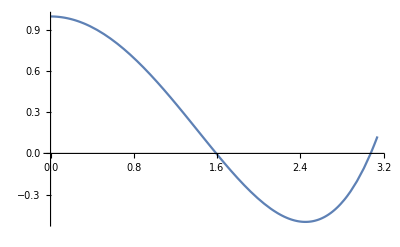

```mathematica
Plot[SerCos[5,x],{x,0,Pi}]
```

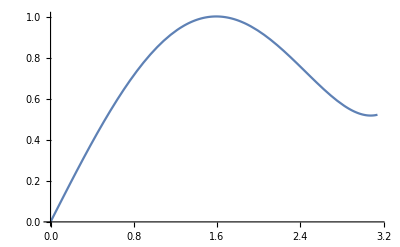

```mathematica
Plot[SerSin[5,x],{x,0,Pi}]
```

```mathematica
N[SerSin[5,3]]
```

0.525

```mathematica
N[Sin[3]]
```

0.14112

```mathematica
N[SerSin[10,3]]
```

0.145313

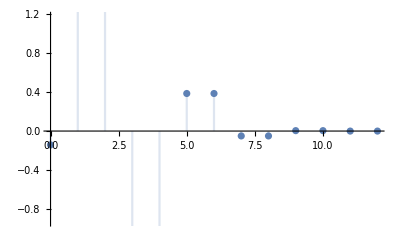

```mathematica
DiscretePlot[SerSin[x,3]-Sin[3],{x,0,12}]
```

Question 2

```mathematica
N[SerCos[2,0.3]^2+SerSin[2,0.3]^2]
```

1.00203

```mathematica
N[SerCos[3,0.3]^2+SerSin[3,0.3]^2]
```

0.999345

```mathematica
SerCos[6,0.3]^2+SerSin[6,0.3]^2
```

1.

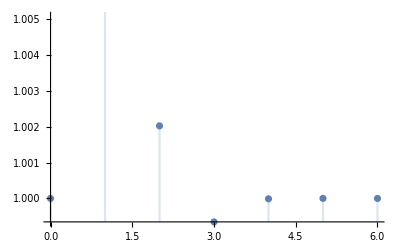

```mathematica
DiscretePlot[SerCos[x,0.3]^2+SerSin[x,0.3]^2,{x,0,6}]
```

We can see that at larger values of n, the series expansions closely approach 1. However, at smaller values of n, there is an error apparent.

```mathematica
SerCosSq[n_,x_]:=Normal[Series[(Cos[t])^2,{t,0,n}]]/.t-> x
```

```mathematica
SerSinSq[n_,x_]:=Normal[Series[(Sin[t])^2,{t,0,n}]]/.t-> x
```

```mathematica
N[SerCosSq[3,0.3]+SerSinSq[3,0.3]]
```

1.

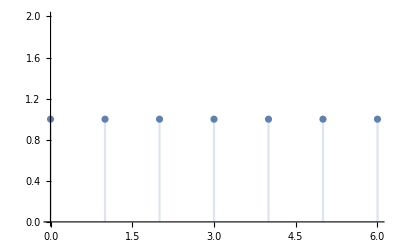

```mathematica
DiscretePlot[SerCosSq[x,0.5]+SerSinSq[x,0.5],{x,0,6}]
```

When using SerCosSq and SerSinSq, we see that the sum is always 1 even for small n. This means that the errors in the approximations between Sin and Cos must be exactly opposed.

#### Part 3

Question 1

```mathematica
Rx[θ_]:={{1,0,0},{0,Cos[θ],-Sin[θ]},{0,Sin[θ],Cos[θ]}}
```

```mathematica
Ry[η_]:={{Cos[η],0,Sin[η]},{0,1,0},{-Sin[η],0,Cos[η]}}
```

```mathematica
Rz[ϕ_]:={{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}}
```

Question 2

```mathematica
Rot3[η_,θ_,ϕ_]:= FullSimplify[Rz[η].Rx[θ].Rz[ϕ]]
```

```mathematica
MatrixForm[Simplify[Rot3[η,θ,ϕ]]]
```

(Cos[η] Cos[ϕ]-Cos[θ] Sin[η] Sin[ϕ] | -Cos[θ] Cos[ϕ] Sin[η]-Cos[η] Sin[ϕ] | Sin[η] Sin[θ]
Cos[ϕ] Sin[η]+Cos[η] Cos[θ] Sin[ϕ] | Cos[η] Cos[θ] Cos[ϕ]-Sin[η] Sin[ϕ] | -Cos[η] Sin[θ]
Sin[θ] Sin[ϕ] | Cos[ϕ] Sin[θ] | Cos[θ])

Question 3

```mathematica
Rot3Inverse[η_,θ_,ϕ_]:=Rz[-ϕ].Rx[-θ].Rz[-η]
```

```mathematica
MatrixForm[Simplify[Rot3Inverse[η,θ,ϕ].Rot3[η,θ,ϕ]]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Question 4

```mathematica
MatrixForm[Simplify[Inverse[Rot3[η,θ,ϕ]].Rot3[η,θ,ϕ]]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
MatrixForm[Simplify[Inverse[Rot3[η,θ,ϕ]]-Rot3Inverse[η,θ,ϕ]]]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)